```mathematica
ClearAll["Global`*"]
NotebookDirectory[] ;
SetDirectory[%];
```

```mathematica
udata=ReadList["Geff.dat", {Number,Number}];
cdatah=ReadList["cdatah.txt",{Number,Number}];
```

```mathematica
rudata=Join[udata,cdatah];
```

```mathematica
u=Interpolation[rudata];
ru[r_]:=Piecewise[{{1,0≤r<0.01},{u[r],0.01<=r≤201.5},{1,r>201.5}}];
```

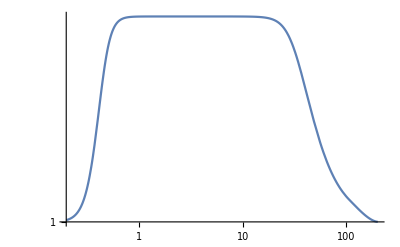

```mathematica
LogLogPlot[ru[r],{r,0,201.5}]
```

```mathematica
du=D[u[r],r];
rdu[r_]:=Piecewise[{{0,0≤r<0.01},{du,0.01<=r≤201.5},{0,r>201.5}}]
```

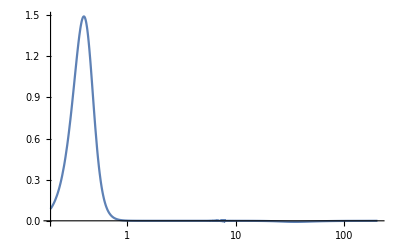

```mathematica
LogLinearPlot[rdu[r],{r,0,201.5},PlotRange->All]
```

```mathematica
(*rdudata=Table[{x,rdu[x]},{x,0,1,0.01}];
rduf=Interpolation[rdudata];
rrduf[r_]:=Piecewise[{{rduf[r],0<=r≤1},{0,r>1}}]*)
```

```mathematica
(*LogLinearPlot[rrduf[r],{r,0,201.5},PlotRange->All]*)
```

```mathematica
rg[r_]:=1;
(*r01=0.01;alpha2=1;beta2=1;alpha1=1.1;beta1=1.1;
 pmu[r_]:=(1+alpha1*(r/r01)^2)/(1+alpha2*(r/r01)^2);
pgamma[r_]:=(1+beta1*(r/r01)^2)/(1+beta2*(r/r01)^2);
Sigma[r_]:=((1+pgamma[r])*pmu[r])/2;*)
```

```mathematica
r01=0.1;w01=0.01;alpha1=1.1;alpha2=1;r02=50;
```

```mathematica
Sigma0[r_]:=(1+alpha1*((r-r01)/w01)^2)/(1+alpha2*((r-r01)/w01)^2);
```

```mathematica
Sigma[r_]:=Piecewise[{{1,0≤r<r01},{Sigma0[r],r01≤r<=r02},{1,r>r02}}];
```

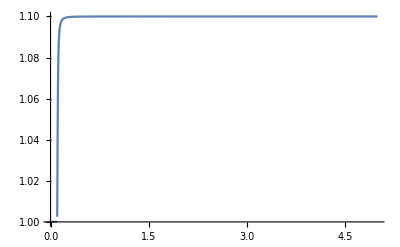

```mathematica
Plot[Sigma[r],{r,0,5},PlotRange->All]
```

```mathematica
Sigma[0.]
```

1

```mathematica
dSigma0[r_]:=D[Sigma0[a],a]/.a->r
```

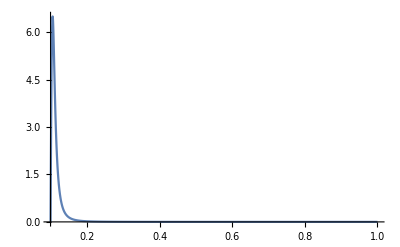

```mathematica
Plot[dSigma0[r],{r,r01,1},PlotRange->All]
```

```mathematica
dSigma0[r01]
```

0.

```mathematica
dSigma[r_]:=Piecewise[{{0,0≤r<r01},{dSigma0[r],r01<=r≤r02},{0,r>r02}}]
```

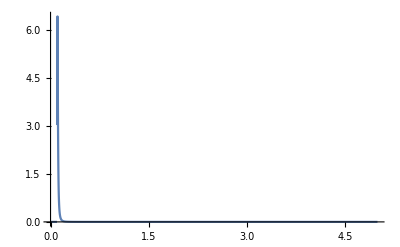

```mathematica
Plot[dSigma[r],{r,0,5},PlotRange->All]
```

```mathematica
dSigma[r01-0.001]
```

0

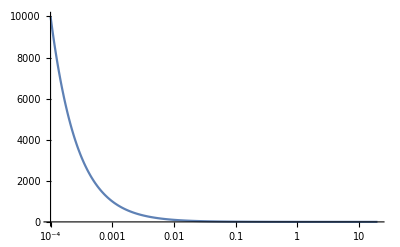

```mathematica
a1[b_]:=b*NIntegrate[Sigma[r]/r^3/.r->√(b^2+z^2),{z,0,∞}]
LogLinearPlot[a1[b],{b,0.0001,20},PlotRange->All]
```

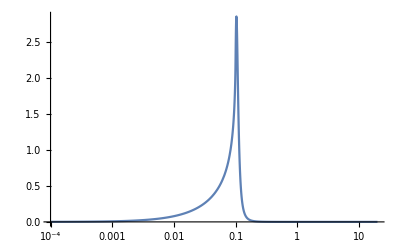

```mathematica
a2[b_]:=b*NIntegrate[dSigma[r]/r^2/.r->√(b^2+z^2),{z,0,Infinity}]
LogLinearPlot[a2[b],{b,0.0001,20},PlotRange->All]
```

```mathematica
(*a3[b_]:=b*NIntegrate[(ru[r]*rdu[r])/r^2/.r->√(b^2+z^2),{z,0,Infinity}]
LogLinearPlot[a3[b],{b,0.0001,201.5},PlotRange->All]*)
```

```mathematica
Ib[b_]:=a1[b]-a2[b];
```

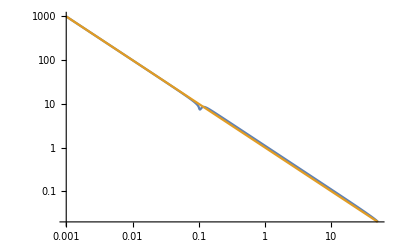

```mathematica
LogLogPlot[{Ib[b],1/b},{b,0.001,50}]
```

```mathematica
Ibdata1=Table[{b,a1[b]-a2[b]},{b,0.001,1,0.001}];
Ibdata2=Table[{b,a1[b]-a2[b]},{b,1.01,50,0.01}];
```

```mathematica
Ibdata3=Table[{b,a1[b]-a2[b]},{b,0.00101,0.00199,0.00001}];
```

```mathematica
Ibdatan=Join[Ibdata1,Ibdata2,Ibdata3];
```

```mathematica
Ibdata=Sort[Ibdatan,#1[[1]]<#2[[1]]&];
```

```mathematica
Export["Ibdata.txt",Ibdata,"Table"];
```

```mathematica
Ibdata=ReadList["Ibdata.txt",{Number,Number}];
```

```mathematica
rIb=Interpolation[Ibdata];
```

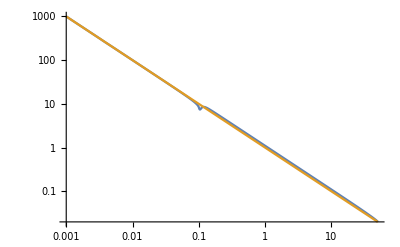

```mathematica
rrIb[b_]:=Piecewise[{{-rIb[-b],-50≤b≤-0.001},{1/b,-0.001<b<0.001},{rIb[b],0.001<=b≤50}}];
LogLogPlot[{rrIb[b],1/b},{b,0.001,50},PlotRange->All]
```

```mathematica
(*LogLogPlot[{a1[b]-a2[b]-a3[b],rrIb[b]},{b,0.01,110},PlotRange->All]*)
```

```mathematica
(*LogLogPlot[{rrIb[b],2/b},{b,0.001,201.5},PlotRange->All]*)
```

```mathematica
Itbdata=Table[{Ibdata[[i,1]],Ibdata[[i,2]]/Ibdata[[i,1]]},{i,1,Length[Ibdata]}];
```

```mathematica
Export["Itbdata.txt",Itbdata,"Table"];
```

```mathematica
Itbdata=ReadList["Itbdata.txt",{Number,Number}];
```

```mathematica
rItb=Interpolation[Itbdata];
```

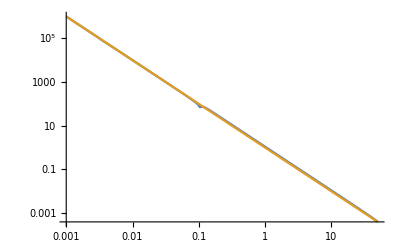

```mathematica
rrItb[b_]:=Piecewise[{{rItb[-b],-50≤b≤-0.001},{1/b^2,-0.001<b<0.001},{rItb[b],0.001<=b≤50}}];
LogLogPlot[{rrItb[b],1/b^2},{b,0.001,50},PlotRange->All]
```

```mathematica
(*LogLogPlot[{rrItb[b],2/b^2},{b,0.001,201.5},PlotRange->All]*)
```

```mathematica
zl=0.3;
zs=1;
om=0.3;
h0=67.8;(*km s^-1 Mpc^-1*)
h0c=69.6;(*km s^-1 Mpc^-1*)
c=3*10^5;(*km s^-1*)
(*Mpc=30.85678*10^18 km*)
(*Msun=1.9891*10^30 kg*)
(*G=6.673*10^-11 m^3 kg^-1 s^-2*)
G=6.673*10^-20*1.9891*10^30;(*km^3 Msun^-1 s^-2*)
M=10^12;(*Msun*)
```

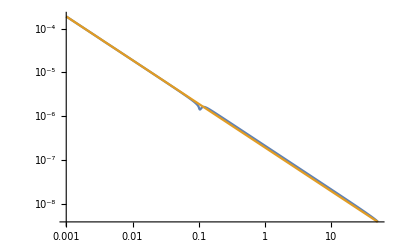

```mathematica
LogLogPlot[{(4G*M)/c^2*1/(30.85678*10^18)*rrIb[b],(4G*M)/c^2*1/(30.85678*10^18)*1/b},{b,0.001,50},PlotRange->All]
```

```mathematica
H[t_]:=Sqrt[1-om+om *(1+t)^3];
DA[z_]:=c/h0 1/(1+z)NIntegrate[1/H[t],{t,0,z}];
DAc[z_]:=c/h0c 1/(1+z)NIntegrate[1/H[t],{t,0,z}];
DA2[z1_,z2_]:=c/h0 1/(1+z2)NIntegrate[1/H[t],{t,z1,z2}];
DA2c[z1_,z2_]:=c/h0c 1/(1+z2)NIntegrate[1/H[t],{t,z1,z2}];

DA[zl]
DA[zs]
DA2[zl,zs]
DA2[zl,zs]/(DA[zl]*DA[zs])

DAc[zl]
DAc[zs]
DA2c[zl,zs]
DA2c[zl,zs]/(DAc[zl]*DAc[zs])
```

949.236

1706.7

1089.69

0.000672626

924.687

1662.56

1061.51

0.000690484

```mathematica
thetaE=√((4G*M)/c^2*1/(30.85678*10^18)*DA2[zl,zs]/(DA[zl]*DA[zs]))
thetaEc=√((4G*M)/c^2*1/(30.85678*10^18)*DA2c[zl,zs]/(DAc[zl]*DAc[zs]))
thetaE*DA[zl]
```

0.0000113399

0.0000114894

0.0107642

```mathematica
n=2000;
```

```mathematica
thetaGRpd=Table[0,{n}];
thetaGRmd=Table[0,{n}];
thetaGRcpd=Table[0,{n}];
thetaGRcmd=Table[0,{n}];
thetaMGpd=Table[0,{n}];
thetaMGmd=Table[0,{n}];
```

```mathematica
For[i=1,i≤n,i++,If[i≤500,y=0.001*(i-1),y=0.5+0.003*(i-501)];thetaGR=theta/.NSolve[theta-y*thetaE==(4G*M)/c^2*1/(30.85678*10^18)*DA2[zl,zs]/(DA[zs]DA[zl])*1/theta,theta];thetaGRc=theta/.NSolve[theta-y*thetaE==(4G*M)/c^2*1/(30.85678*10^18)*DA2c[zl,zs]/(DAc[zs]DAc[zl])*1/theta,theta];
thetaGRp=thetaGR[[1]];
thetaGRm=thetaGR[[2]];
thetaGRpd[[i]]={y,thetaGRp};
thetaGRmd[[i]]={y,thetaGRm};
thetaGRcp=thetaGRc[[1]];
thetaGRcm=thetaGRc[[2]];
thetaGRcpd[[i]]={y,thetaGRcp};
thetaGRcmd[[i]]={y,thetaGRcm};
thetaMGp=theta/.FindRoot[theta-y*thetaE==DA2[zl,zs]/DA[zs]*(4G*M)/c^2*1/(30.85678*10^18)*rrIb[DA[zl]*theta],{theta,thetaGRp}];
thetaMGm=theta/.FindRoot[theta-y*thetaE==DA2[zl,zs]/DA[zs]*(4G*M)/c^2*1/(30.85678*10^18)*rrIb[DA[zl]*theta],{theta,thetaGRm}];
thetaMGpd[[i]]={y,thetaMGp};
thetaMGmd[[i]]={y,thetaMGm};]
```

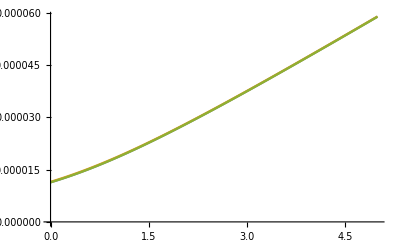

```mathematica
ListPlot[{thetaGRpd,thetaGRcpd,thetaMGpd},Joined->True,PlotRange->All]
```

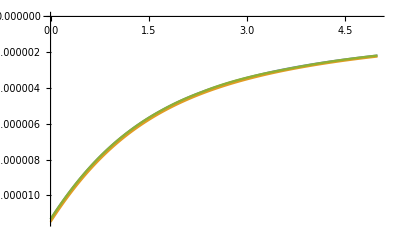

```mathematica
ListPlot[{thetaGRmd,thetaGRcmd,thetaMGmd},Joined->True,PlotRange->All]
```

```mathematica
(*thetaGRpd=ReadList["thetaGRpd.txt",{Number,Number}];
thetaGRmd=ReadList["thetaGRmd.txt",{Number,Number}];
thetaGRcpd=ReadList["thetaGRcpd.txt",{Number,Number}];
thetaGRcmd=ReadList["thetaGRcmd.txt",{Number,Number}];
thetaMGpd=ReadList["thetaMGpd.txt",{Number,Number}];
thetaMGmd=ReadList["thetaMGmd.txt",{Number,Number}];*)
```

```mathematica
min1=Min[Table[thetaMGpd[[i,2]],{i,1,n}]]
```

0.0000113371

```mathematica
max1=Max[Table[thetaMGpd[[i,2]],{i,1,n}]]
```

0.0000588183

```mathematica
min2=Min[Table[thetaMGmd[[i,2]],{i,1,n}]]
```

-0.0000113371

```mathematica
max2=Max[Table[thetaMGmd[[i,2]],{i,1,n}]]
```

-2.1851×10^-6

```mathematica
xmin=Min[Abs[min1],Abs[min2],Abs[max1],Abs[max2]]
```

2.1851×10^-6

```mathematica
xmax=Max[Abs[min1],Abs[min2],Abs[max1],Abs[max2]]
```

0.0000588183

```mathematica
phihGR[x_]:=(4G*M)/c^2*1/(30.85678*10^18)*DA2[zl,zs]/(DA[zl]*DA[zs])Log[Abs[x]];
phihGRc[x_]:=(4G*M)/c^2*1/(30.85678*10^18)*DA2c[zl,zs]/(DAc[zl]*DAc[zs])Log[Abs[x]];
phihMGini[x_]:=NIntegrate[DA2[zl,zs]/DA[zs]*(4*G*M)/c^2*1/(30.85678*10^18)*rrIb[b]/.b->(DA[zl]*theta),{theta,xmin,x}];
phihMG[x_]:=phihMGini[Abs[x]];
```

```mathematica
TDGR=Table[0,{n}];
TDGRc=Table[0,{n}];
TDMG=Table[0,{n}];
```

```mathematica
For[i=1,i≤n,i++,thetaGRp=thetaGRpd[[i,2]];y=thetaGRpd[[i,1]];thetaGRm=thetaGRmd[[i,2]];
alphaGRp=thetaGRp-y*thetaE;
alphaGRm=thetaGRm-y*thetaE;
DettGR=(1+zl)/c*30.85678*10^18*(DA[zl]*DA[zs])/DA2[zl,zs](1/2(alphaGRm)^2-1/2(alphaGRp)^2-(phihGR[thetaGRm]-phihGR[thetaGRp]));
TDGR[[i]]={y,DettGR};

thetaGRcp=thetaGRcpd[[i,2]];y=thetaGRcpd[[i,1]];thetaGRcm=thetaGRcmd[[i,2]];
alphaGRcp=thetaGRcp-y*thetaE;
alphaGRcm=thetaGRcm-y*thetaE;
DettGRc=(1+zl)/c*30.85678*10^18*(DAc[zl]*DAc[zs])/DA2c[zl,zs](1/2(alphaGRcm)^2-1/2(alphaGRcp)^2-(phihGRc[thetaGRcm]-phihGRc[thetaGRcp]));
TDGRc[[i]]={y,DettGRc};
thetaMGp=thetaMGpd[[i,2]];y=thetaMGpd[[i,1]];thetaMGm=thetaMGmd[[i,2]];
alphaMGp=thetaMGp-y*thetaE;
alphaMGm=thetaMGm-y*thetaE;
DettMG=(1+zl)/c*30.85678*10^18*(DA[zl]*DA[zs])/DA2[zl,zs](1/2 alphaMGm^2-1/2 alphaMGp^2-(phihMG[thetaMGm]-phihMG[thetaMGp]));
TDMG[[i]]={y,DettMG};]
```

```mathematica
(*TDMG=ReadList["TDMG.txt",{Number,Number}];*)
```

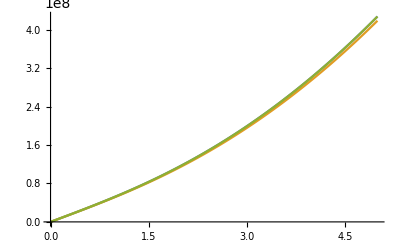

```mathematica
ListPlot[{TDGR,TDGRc,TDMG},Joined->True,PlotRange->All]
```

```mathematica
diffhc=Table[{TDGR[[i,1]],(TDGRc[[i,2]]-TDGR[[i,2]])/TDGR[[i,2]]},{i,2,Length[TDMG]}];
diffMG=Table[{TDGR[[i,1]],(TDMG[[i,2]]-TDGR[[i,2]])/TDGR[[i,2]]},{i,2,Length[TDMG]}];
(*diffMGc=Table[{TDGRt[[i,1]],(TDMGt[[i,2]]-TDGRct[[i,2]])},{i,1,Length[TDMGt]}];*)
```

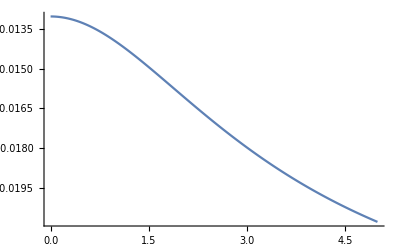

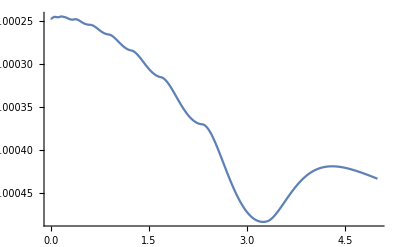

```mathematica
ListLinePlot[diffhc]
ListLinePlot[diffMG]
(*ListLinePlot[diffMGc]*)
```

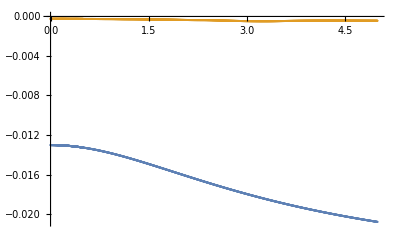

```mathematica
ListPlot[{diffhc,diffMG},PlotRange->All]
```

```mathematica
Export["thetaGRpd.txt",thetaGRpd,"Table"];
Export["thetaGRcpd.txt",thetaGRcpd,"Table"];
Export["thetaMGpd.txt",thetaMGpd,"Table"];
Export["thetaGRmd.txt",thetaGRmd,"Table"];
Export["thetaGRcmd.txt",thetaGRcmd,"Table"];
Export["thetaMGmd.txt",thetaMGmd,"Table"];
```

```mathematica
Export["TDGR.txt",TDGR,"Table"];
Export["TDGRc.txt",TDGRc,"Table"];
Export["TDMG.txt",TDMG,"Table"];
```

```mathematica
ClearAll["Global`*"]
NotebookDirectory[] ;
SetDirectory[%];
```

```mathematica
Itbdata=ReadList["Itbdata.txt",{Number,Number}];
```

```mathematica
rItb=Interpolation[Itbdata];
```

```mathematica
rrItb[b_]:=Piecewise[{{rItb[-b],-50≤b≤-0.001},{1/b^2,-0.001<b<0.001},{rItb[b],0.001<=b≤50}}];
```

```mathematica
LogLogPlot[{rrItb[b],1/b^2},{b,0.001,50},PlotRange->All]
```

-Graphics-

```mathematica
zl=0.3;
zs=1;
om=0.3;
h0=67.8;(*km s^-1 Mpc^-1*)
h0c=69.6;(*km s^-1 Mpc^-1*)
c=3*10^5;(*km s^-1*)
(*Mpc=30.85678*10^18 km*)
(*Msun=1.9891*10^30 kg*)
(*G=6.673*10^-11 m^3 kg^-1 s^-2*)
G=6.673*10^-20*1.9891*10^30;(*km^3 Msun^-1 s^-2*)
M=10^12;(*Msun*)
sigmav=300;(*km s^-1*)
SISlim=0.01;(*Mpc*)
```

```mathematica
H[t_]:=Sqrt[1-om+om *(1+t)^3];
DA[z_]:=c/h0 1/(1+z)NIntegrate[1/H[t],{t,0,z}];
DAc[z_]:=c/h0c 1/(1+z)NIntegrate[1/H[t],{t,0,z}];
DA2[z1_,z2_]:=c/h0 1/(1+z2)NIntegrate[1/H[t],{t,z1,z2}];
DA2c[z1_,z2_]:=c/h0c 1/(1+z2)NIntegrate[1/H[t],{t,z1,z2}];

DA[zl]
DA[zs]
DA2[zl,zs]
DA2[zl,zs]/(DA[zl]*DA[zs])

DAc[zl]
DAc[zs]
DA2c[zl,zs]
DA2c[zl,zs]/(DAc[zl]*DAc[zs])
```

949.236

1706.7

1089.69

0.000672626

924.687

1662.56

1061.51

0.000690484

```mathematica
thetaE=(4Pi*sigmav^2)/c^2*DA2[zl,zs]/DA[zs]
thetaEc=(4Pi*sigmav^2)/c^2*DA2c[zl,zs]/DAc[zs]
thetaE*DA[zl]
```

8.02339×10^-6

8.02339×10^-6

0.00761609

```mathematica
rhoSIS[r_]:=sigmav^2/(2*Pi*G)*30.85678*10^18*1/r^2;
```

```mathematica
SigmaSIS[ksi_]:=sigmav^2/(2*G)*30.85678*10^18*1/ksi;
```

```mathematica
alphaSISGR0[ksi_]:=(4Pi*sigmav^2)/c^2*DA2[zl,zs]/DA[zs];
```

```mathematica
alphaSISGR0[0]
```

8.02339×10^-6

```mathematica
MSIS=(sigmav^2*Pi)/G*30.85678*10^18*SISlim
```

6.57302×10^11

```mathematica
alphaSISGR[ksi_]:=Piecewise[{{-(4Pi*sigmav^2)/c^2*DA2[zl,zs]/DA[zs],-SISlim≤ksi<0},{(4Pi*sigmav^2)/c^2*DA2[zl,zs]/DA[zs],0<=ksi≤SISlim},{4 G/c^2*1/(30.85678*10^18)*MSIS/ksi*DA2[zl,zs]/DA[zs],Abs[ksi]>SISlim}}];
```

```mathematica
(*alphaSISGRcal[ksi_]:=DA2[zl,zs]/DA[zs]*(4*G)/c^2*1/(30.85678*10^18)*NIntegrate[ksiSigmaSISana[ksip]*(ksi-ksip*Cos[phi])*(ksi^2+ksip^2-2ksi*ksip*Cos[phi])^-1,{phi,0,2Pi},{ksip,0,SISlim}];*)
```

```mathematica
(*LogLogPlot[{alphaSISGR0[ksi],alphaSISGR[ksi],alphaSISGRcal[ksi]},{ksi,0.001,20}]*)
```

```mathematica
(*rhoSISMG[r_]:=sigmav^2/(2*Pi*G)*30.85678*10^18*1/(ru[r]*r^2);*)
```

```mathematica
(*SigmaSISMG[ksi_]:=2NIntegrate[rhoSISMG[r]/.r->(ksi^2+z^2)^(1/2),{z,0,Infinity}];*)
```

```mathematica
(*SigmaSISMGana[ksi_]:=Piecewise[{{sigmav^2/(Pi*G)*30.85678*10^18*1/ksi*(ArcTan[((0.4^2-ksi^2)^(1/2))/ksi]+3/4 ArcTan[((48.9^2-ksi^2)^(1/2))/ksi]-3/4*ArcTan[((0.4^2-ksi^2)^(1/2))/ksi]+Pi/2-ArcTan[((48.9^2-ksi^2)^(1/2))/ksi]),0<=ksi<0.4},{sigmav^2/(Pi*G)*30.85678*10^18*1/ksi*(3/4 ArcTan[((48.9^2-ksi^2)^(1/2))/ksi]+Pi/2-ArcTan[((48.9^2-ksi^2)^(1/2))/ksi]),0.4≤ksi≤48.9},{sigmav^2/(Pi*G)*30.85678*10^18*1/ksi*Pi/2,ksi>48.9}}];*)
```

```mathematica
(*Plot[{SigmaSISGR[ksi],SigmaSISMG[ksi],SigmaSISMGana[ksi]},{ksi,0.001,10}]*)
```

```mathematica
ksiSigmaSISana[ksi_]:=sigmav^2/(2*G)*30.85678*10^18;
```

```mathematica
alphaSISMG[ksi_]:=DA2[zl,zs]/DA[zs]*(4*G)/c^2*1/(30.85678*10^18)*NIntegrate[ksiSigmaSISana[ksip]*(ksi-ksip*Cos[phi])*rrItb[(ksi^2+ksip^2-2ksi*ksip*Cos[phi])^(1/2)],{phi,0,2Pi},{ksip,0,SISlim}];
```

```mathematica
alphaSISMG[0.005]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {0.99999873896038742975964213883892373058159819265711121261119842529,0.499999}. NIntegrate obtained 6.55709×10^13 and 4.31749×10^8 for the integral and error estimates.

8.00394×10^-6

```mathematica
(*ListLogLogPlot[{Table[{ksi,alphaSISGR0[ksi]},{ksi,0.001,0.1,0.001}],Table[{ksi,alphaSISGR[ksi]},{ksi,0.001,0.1,0.001}],Table[{ksi,alphaSISMG[ksi]},{ksi,0.001,0.1,0.001}]},PlotRange->All]*)
```

```mathematica
alphaSISMGdata1=Table[{ksi,alphaSISMG[ksi]},{ksi,0.0001,0.00099,0.00001}];
alphaSISMGdata2=Table[{ksi,alphaSISMG[ksi]},{ksi,0.001,0.0099,0.0001}];
alphaSISMGdata3=Table[{ksi,alphaSISMG[ksi]},{ksi,0.01,1,0.001}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {1.26104×10^-6,0.0909113}. NIntegrate obtained 6.5729×10^13 and 1.12959×10^10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {0.99999873896038742975964213883892373058159819265711121261119842529,0.0991014}. NIntegrate obtained 6.57306×10^13 and 6.39155×10^9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {0.99999873896038742975964213883892373058159819265711121261119842529,0.107143}. NIntegrate obtained 6.573×10^13 and 6.72842×10^9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {1.26104×10^-6,0.500003}. NIntegrate obtained 6.57322×10^13 and 4.56238×10^8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {1.26104×10^-6,0.500003}. NIntegrate obtained 6.5733×10^13 and 1.36233×10^9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {1.26104×10^-6,0.499999}. NIntegrate obtained 6.57338×10^13 and 1.13624×10^9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
alphaSISMGdata4=Table[{ksi,alphaSISMG[ksi]},{ksi,0.00001,0.00009,0.00001}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {1.26104×10^-6,0.00990087}. NIntegrate obtained 6.57301×10^13 and 5.8018×10^9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {0.99999873896038742975964213883892373058159819265711121261119842529,0.0196076}. NIntegrate obtained 6.57294×10^13 and 4.29945×10^9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in phi near {phi,ksip} = {0.466029,0.000103042}. NIntegrate obtained 6.57304×10^13-0.0881397 ⅈ and 1.54362×10^9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
alphaSISMGdata5=Table[{ksi,alphaSISMG[ksi]},{ksi,0.000001,0.000009,0.000001}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {1.26104×10^-6,0.000999059}. NIntegrate obtained 6.5731×10^13 and 1.00298×10^10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {1.26104×10^-6,0.00199608}. NIntegrate obtained 6.57312×10^13 and 7.46109×10^9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ksip near {phi,ksip} = {1.26104×10^-6,0.00299107}. NIntegrate obtained 6.57329×10^13 and 1.09571×10^10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
(*alphaSISMGdata6=Table[{ksi,alphaSISMG[ksi]},{ksi,1.1,10,0.1}];*)
```

```mathematica
(*alphaSISMGdata7=Table[{ksi,alphaSISMG[ksi]},{ksi,10,500,10}];*)
```

```mathematica
alphaSISMGdata=Join[alphaSISMGdata5,alphaSISMGdata4,alphaSISMGdata1,alphaSISMGdata2,alphaSISMGdata3];
```

```mathematica
Export["alphaSISMGdata.txt",alphaSISMGdata,"Table"]
```

alphaSISMGdata.txt

```mathematica
alphaSISMGdata=ReadList["alphaSISMGdata.txt",{Number,Number}];
```

```mathematica
(*ListLogLogPlot[{alphaSISMGdata,Table[{x,alphaSISGR[x]},{x,0,1,0.00001}]}]*)
```

```mathematica
alphaSISMGf=Interpolation[alphaSISMGdata];
```

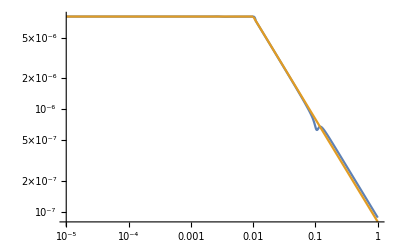

```mathematica
LogLogPlot[{alphaSISMGf[r],alphaSISGR[r]},{r,10^-5,1},PlotRange->All]
```

```mathematica
ralphaSISMGf[r_]:=Piecewise[{{-alphaSISMGf[-r],-1≤r≤-10^-5},{-thetaE,-10^-5<r<0},{thetaE,0≤r<10^-5},{alphaSISMGf[r],10^-5<=r<=1}}];
```

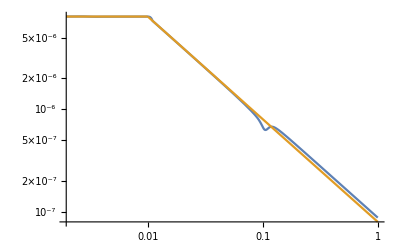

```mathematica
LogLogPlot[{ralphaSISMGf[r],alphaSISGR[r]},{r,-1,1},PlotRange->All]
```

```mathematica
n=2000;
```

```mathematica
thetaGRpd=Table[0,{n}];
thetaGRmd=Table[0,{n}];
thetaGRcpd=Table[0,{n}];
thetaGRcmd=Table[0,{n}];
thetaMGpd=Table[0,{n}];
thetaMGmd=Table[0,{n}];
```

```mathematica
thetaGRtest=theta/.NSolve[theta-0*thetaE==alphaSISGR[DA[zl]*theta],theta]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-8.02339×10^-6,8.02339×10^-6}

```mathematica
For[i=1,i≤n,i++,y=0.0005*(i-1);
thetaGR=theta/.NSolve[theta-y*thetaE==alphaSISGR[DA[zl]*theta],theta];(*thetaGRc=theta/.NSolve[theta-y*thetaE==(4G*M)/c^2*1/(30.85678*10^18)*DA2c[zl,zs]/(DAc[zs]DAc[zl])*1/theta,theta];*)
thetaGRp=thetaGR[[2]];
thetaGRm=thetaGR[[1]];
thetaGRpd[[i]]={y,thetaGRp};
thetaGRmd[[i]]={y,thetaGRm};
(*thetaGRcp=y*thetaE+thetaEc;
thetaGRcm=y*thetaE-thetaEc;*)
thetaGRcpd[[i]]={y,thetaGRp};
thetaGRcmd[[i]]={y,thetaGRm};
thetaMGp=theta/.FindRoot[theta-y*thetaE==ralphaSISMGf[DA[zl]*theta],{theta,thetaGRp}];
thetaMGm=theta/.FindRoot[theta-y*thetaE==ralphaSISMGf[DA[zl]*theta],{theta,thetaGRm}];
thetaMGpd[[i]]={y,thetaMGp};
thetaMGmd[[i]]={y,thetaMGm};]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

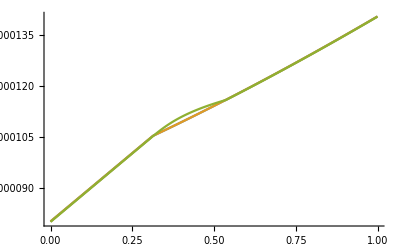

```mathematica
ListPlot[{thetaGRpd,thetaGRcpd,thetaMGpd},Joined->True,PlotRange->All]
```

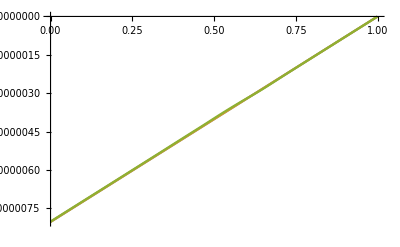

```mathematica
ListPlot[{thetaGRmd,thetaGRcmd,thetaMGmd},Joined->True,PlotRange->All]
```

```mathematica
min1=Min[Table[thetaGRpd[[i,2]],{i,1,n}],Table[thetaMGpd[[i,2]],{i,1,n}]]
```

8.00997×10^-6

```mathematica
max1=Max[Table[thetaGRpd[[i,2]],{i,1,n}],Table[thetaMGpd[[i,2]],{i,1,n}]]
```

0.0000140398

```mathematica
min2=Min[Table[thetaGRmd[[i,2]],{i,1,n}],Table[thetaMGmd[[i,2]],{i,1,n}]]
```

-8.02339×10^-6

```mathematica
max2=Max[Table[thetaGRmd[[i,2]],{i,1,n}],Table[thetaMGmd[[i,2]],{i,1,n}]]
```

-4.01169×10^-9

```mathematica
minx=Min[Abs[min1],Abs[min2],Abs[max1],Abs[max2]]
```

4.01169×10^-9

```mathematica
maxx=Max[Abs[min1],Abs[min2],Abs[max1],Abs[max2]]
```

0.0000140398

```mathematica
phihGRini[x_]:=NIntegrate[alphaSISGR[DA[zl]*theta],{theta,minx,x}];
phihGR[x_]:=phihGRini[Abs[x]];
phihGRc[x_]:=phihGR[x];
phihMGini[x_]:=NIntegrate[ralphaSISMGf[DA[zl]*theta],{theta,minx,x}];
phihMG[x_]:=phihMGini[Abs[x]];
```

```mathematica
TDGR=Table[0,{n}];
TDGRc=Table[0,{n}];
TDMG=Table[0,{n}];
```

```mathematica
For[i=1,i≤n,i++,thetaGRp=thetaGRpd[[i,2]];y=thetaGRpd[[i,1]];thetaGRm=thetaGRmd[[i,2]];
alphaGRp=thetaGRp-y*thetaE;
alphaGRm=thetaGRm-y*thetaE;
DettGR=(1+zl)/c*30.85678*10^18*(DA[zl]*DA[zs])/DA2[zl,zs](1/2 alphaGRm^2-1/2 alphaGRp^2-(phihGR[thetaGRm]-phihGR[thetaGRp]));
TDGR[[i]]={y,DettGR};

thetaGRcp=thetaGRcpd[[i,2]];y=thetaGRcpd[[i,1]];thetaGRcm=thetaGRcmd[[i,2]];
alphaGRcp=thetaGRcp-y*thetaE;
alphaGRcm=thetaGRcm-y*thetaE;
DettGRc=(1+zl)/c*30.85678*10^18*(DAc[zl]*DAc[zs])/DA2c[zl,zs](1/2 alphaGRcm^2-1/2 alphaGRcp^2-(phihGRc[thetaGRcm]-phihGRc[thetaGRcp]));
TDGRc[[i]]={y,DettGRc};
thetaMGp=thetaMGpd[[i,2]];y=thetaMGpd[[i,1]];thetaMGm=thetaMGmd[[i,2]];
alphaMGp=thetaMGp-y*thetaE;
alphaMGm=thetaMGm-y*thetaE;
DettMG=(1+zl)/c*30.85678*10^18*(DA[zl]*DA[zs])/DA2[zl,zs](1/2 alphaMGm^2-1/2 alphaMGp^2-(phihMG[thetaMGm]-phihMG[thetaMGp]));
TDMG[[i]]={y,DettMG};]
```

```mathematica
(*TDMG=ReadList["TDMG.txt",{Number,Number}];*)
```

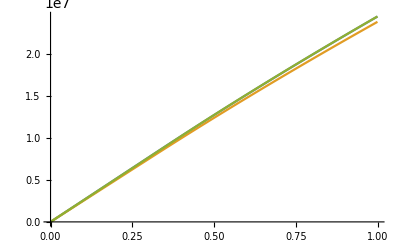

```mathematica
ListPlot[{TDGR,TDGRc,TDMG},Joined->True,PlotRange->All]
```

```mathematica
diffhc=Table[{TDGR[[i,1]],(TDGRc[[i,2]]-TDGR[[i,2]])/TDGR[[i,2]]},{i,2,Length[TDMG]}];
diffMG=Table[{TDGR[[i,1]],(TDMG[[i,2]]-TDGR[[i,2]])/TDGR[[i,2]]},{i,2,Length[TDMG]}];
(*diffMGc=Table[{TDGRt[[i,1]],(TDMGt[[i,2]]-TDGRct[[i,2]])},{i,1,Length[TDMGt]}];*)
```

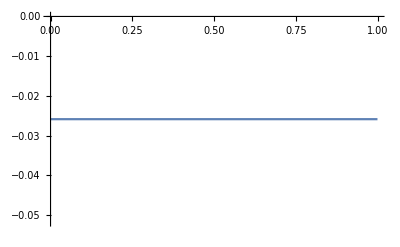

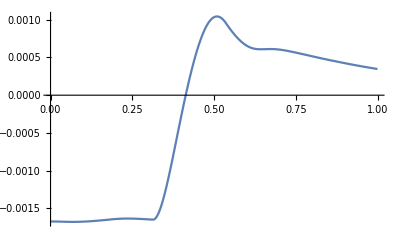

```mathematica
ListLinePlot[diffhc]
ListLinePlot[diffMG]
(*ListLinePlot[diffMGc]*)
```

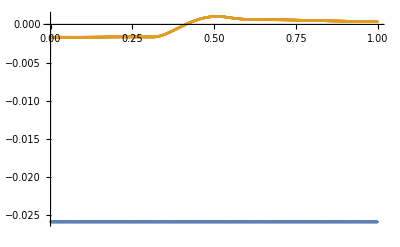

```mathematica
ListPlot[{diffhc,diffMG},PlotRange->All]
```

```mathematica
Export["thetaGRpd_SIS.txt",thetaGRpd,"Table"];
Export["thetaGRcpd_SIS.txt",thetaGRcpd,"Table"];
Export["thetaMGpd_SIS.txt",thetaMGpd,"Table"];
Export["thetaGRmd_SIS.txt",thetaGRmd,"Table"];
Export["thetaGRcmd_SIS.txt",thetaGRcmd,"Table"];
Export["thetaMGmd_SIS.txt",thetaMGmd,"Table"];
```

```mathematica
Export["TDGR_SIS.txt",TDGR,"Table"];
Export["TDGRc_SIS.txt",TDGRc,"Table"];
Export["TDMG_SIS.txt",TDMG,"Table"];
```